```mathematica
(* This Notebook defines modules to find ϕ[n], ϵ[n], η[n], and ns[n]. It does not use the slow roll approx and instead integrates the Klein Gordon equation twice to find ϕ[n]. The first integration uses initial conditions at N=60 from the slow roll approximation. To find the initial conditions for the second integration, we use the solution from the first integration (ϕsol1) to find the value of N where ϵ[n] is 1. Then we set the value of ϕsol1 at that value of N to be the value of ϕ[0] for the initial condition for the second integration. *)
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

```mathematica
(* Define an inflationary potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^4
vp[x_]=v'[x]
ni = 80 (* initial value of n for integration *)
nf = -5 (* final value of n for integration *)
(* Define a module to find ϕi (previously ϕ60) *)
```

4 x^3

80

-5

```mathematica
(* Define a module to find ϕ[ni] in the slow roll approx *)
(* This is used to find the initial conditions for the first integration *)
findϕi[v_,vp_,ni_] := Module[{ϕ0},
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
(*Print["ϕ0 = ",ϕ0];*)
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
ϕi = t/.Last[NSolve[ni==f[t],t]];
Return[ϕi]]
```

```mathematica
ϕi = findϕi[v,vp,ni]
Print["At N=",ni,", ϕi = ",ϕi]
```

25.4558

At N=80, ϕi = 25.4558

```mathematica
(* Define a module to find ϕ[n] using a single integration *)
findϕ[v_,vp_,ϕi_,ni_,nf_] := Module[{h,hsq,ϕpi},
(* Input: v[n], vp[n], ϕi, ni, nf *)
(* Output: ϕsol (a rule) *)
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* find ϕpi = ϕ'[ni] for the second initial condition *)
ϕpi = vp[ϕi]/v[ϕi] ;
(* Solve the Klein-Gordon equation for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)ϕsol = NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi,ϕ'[ni]==ϕpi},ϕ,{n,ni,nf},InterpolationOrder->All];
Return[Last[ϕsol]]]
```

```mathematica
(* Define a module to find ϵ[n], the equation of state *)
findϵ[v_,ϕsol_] := Module[{hsq,ϕp,ϵ},
(* Input: v[n], ϕsol *)
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
Return[ϵ[n]]]
```

NDSolve::ndsz: At n == -3.61444, step size is effectively zero; singularity or stiff system suspected.

{ϕ→InterpolatingFunction[{{-3.61444, 80.}}, <>]}

InterpolatingFunction[{{-3.61444, 80.}}, <>][n]

apple 0.510729

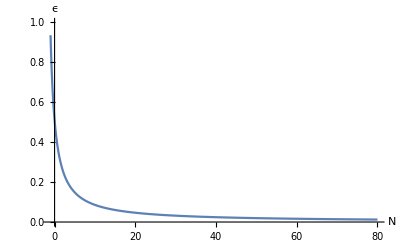

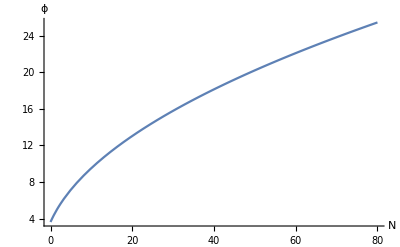

```mathematica
ϕsol = findϕ[v,vp,ϕi,ni,nf]
ϕp[n_] = D[ϕ[n],n]/.ϕsol
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol
ϵ[n] = findϵ[v,ϕsol];
Print["apple ",Evaluate[ϵ[n]/.n->0]]
Plot[Evaluate[ϵ[n]],{n,80,-1},AxesLabel->{N,ϵ},PlotRange->{0,1}]
Plot[Evaluate[ϕ[n]/.ϕsol],{n,80,0},AxesLabel->{N,ϕ}]
```

```mathematica
(* Define a module to find ϕ[n] by integrating twice *)
(* There's something wrong with this module because the ϕ it's returning should be positive and an order of magnitude smaller. I started debugging with the sanity check confirming that the ϕ it returns produces an ϵ that is 1 at n=0. But ϵ[0] does not return a number. I also noticed that if I change the bounds on the NDSolve integration (i.e. change nf to -3, -2, -1, etc.), the nature of the solution changes drastically. I'm not sure what to make of that. *)
findϕ2[v_,vp_,ni_,nf_] := Module[{ϕi,ϕsol1,ϵ1,ϕi1,n1,ϕsol2},
(* Input: v[n], vp[n], ϕi, ni, nf *)
(* Output: ϕsol2 (a rule) *)
ϕi = findϕi[v,vp,ni];
ϕsol1 = findϕ[v,vp,ϕi,ni,nf];
Print["ϕsol1 = ",ϕsol1];
ϵ1[n_]=Last[findϵ[v,ϕsol1]];
Print["ϵ1[0] = ",Evaluate[ϵ1[n]/.n->0]];
Print["Nsolve = ",NSolve[ϵ1[n]==1,n]];
(* n1 = Evaluate[n/.First[NSolve[ϵ1[n]==1,n]]]; *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,-1}]]];(* Finds where ϵ is 1. This is where n should be 0 but isn't due to the approximation. Now we'll use the value of ϕ where ϵ is 1 as the new initial condition at n=0. *)
Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]];
ϕi1 = ϕ[n1]/.ϕsol1;
Print["ϕi1 = ",ϕi1];
ϕsol2 = findϕ[v,vp,ϕi1,0,ni];
Return[ϕsol2]]
```

```mathematica
ϕsol2 = findϕ2[v,vp,ni,nf];
NSolve[ϵ[n]==1,n]
```

NDSolve::ndsz: At n == -3.61444, step size is effectively zero; singularity or stiff system suspected.

ϕsol1 = {ϕ→InterpolatingFunction[{{-3.61444, 80.}}, <>]}

ϵ1[0] = 0.166667

Nsolve = {}

FindRoot::jsing: Encountered a singular Jacobian at the point {n} = {-1.}. Try perturbing the initial point(s).

At n1 = -1., ϵ1 = 0.166667

ϕi1 = 2.45231

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{n→-1.08119},{n→InverseFunction[InterpolatingFunction[{{-3.61444, 80.}}, <>],1,1][-1.41421]}}

```mathematica
ϕi = findϕi[v,vp,ni];
ϕsol = findϕ[v,vp,ϕi,ni,nf] ;
ϵ[n_]:= findϵ[v,ϕsol]
FindRoot[Evaluate[ϵ/.n->nx]-1,{nx,2}]
```

NDSolve::ndsz: At n == -3.61444, step size is effectively zero; singularity or stiff system suspected.

FindRoot::nlnum: The function value {-1. + ϵ} is not a list of numbers with dimensions {1} at {nx} = {2.}.

FindRoot[Evaluate[ϵ/.n→nx]-1,{nx,2}]

```mathematica
FindRoot[Evaluate[ϵ[n]/.n->nx]-1,{nx,2}]
```

InterpolatingFunction::dmval: Input value {-9.40189} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {-9.40189}.

{nx→2.}

```mathematica
Evaluate[ϵ[3.]]
```

(3 (InterpolatingFunction[{{-3.61444, 80.}}, <>][n])^2)/((InterpolatingFunction[{{-3.61444, 80.}}, <>][n])^2+2 (3-1/2 (InterpolatingFunction[{{-3.61444, 80.}}, <>][n])^2))

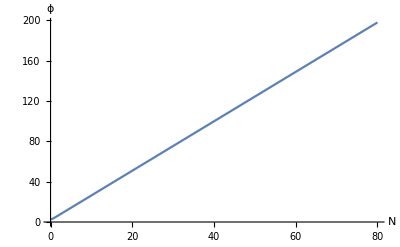

InterpolatingFunction::dmval: Input value {-0.998345} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

ϵ2[40] = 3.

```mathematica
Plot[Evaluate[ϕ[n]/.ϕsol2],{n,80,0},AxesLabel->{N,ϕ}]
ϵ2[n_]=findϵ[v,ϕsol2];
Plot[Evaluate[ϵ2[n]],{n,80,-1},AxesLabel->{N,ϵ2},PlotRange->{0,1}]
Print["ϵ2[40] = ",Evaluate[ϵ2[n]/.n->40]]
```